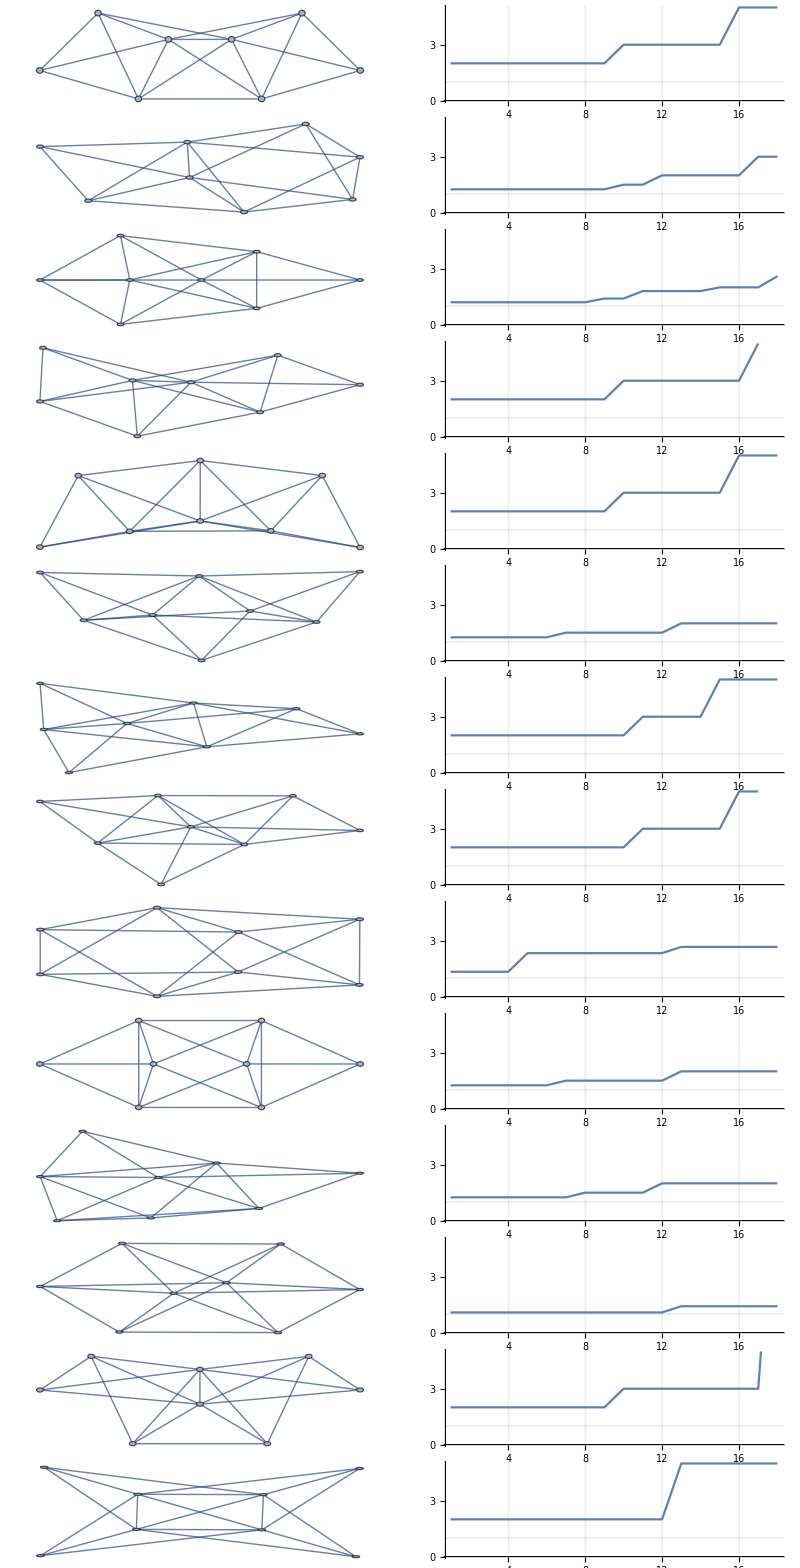
(-Graphics-)

```mathematica
Monitor[
MatrixForm[
Table[
With[
{g=ReadGraph[8,k]},
With[{base=ChromaticPolynomial[g,4]},
{g,ListLinePlot[Sort[Table[ChromaticPolynomial[EdgeDelete[g,e],4]/base,{e,EdgeList[g]}]],GridLines->{Automatic,{{1,{Thick,Red}}}},PlotRange->{All,{0,5}}]}
]
],
{k,14}
]
]
,k]
```

First::normal: Nonatomic expression expected at position 1 in First[Automatic].

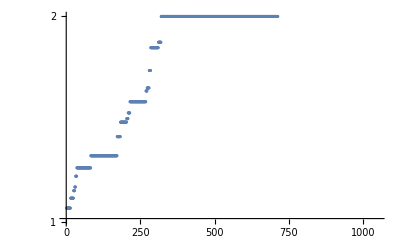

```mathematica
Monitor[
ListLogPlot[
Sort[
Flatten[
Table[
With[
{g=ReadGraph[9,k]},
With[{base=ChromaticPolynomial[g,4]},
Sort[Table[ChromaticPolynomial[EdgeDelete[g,e],4]/base,{e,EdgeList[g]}]]
]
],
{k,50}
],
1
]
]
,PlotRange->{Automatic,{0,2}}
]
,k]
```

```mathematica
Monitor[
Sort[
Tally[
Flatten[
Table[
With[
{g=ReadGraph[10,k]},
With[{base=ChromaticPolynomial[g,4]},
Sort[Table[ChromaticPolynomial[EdgeDelete[g,e],4]/base,{e,EdgeList[g]}]]
]
],
{k,233}
],
1
]
]
]
,k]
```

{{45/44,16},{29/28,4},{22/21,12},{15/14,2},{14/13,1},{13/12,77},{12/11,4},{23/21,2},{11/10,2},{10/9,14},{9/8,8},{8/7,2},{7/6,38},{33/28,12},{6/5,189},{17/14,16},{11/9,2},{16/13,8},{5/4,424},{9/7,12},{17/13,2},{37/28,8},{4/3,73},{15/11,8},{11/8,8},{18/13,4},{7/5,90},{17/12,39},{10/7,4},{13/9,21},{19/13,6},{65/44,8},{3/2,285},{14/9,13},{11/7,8},{8/5,6},{23/14,12},{5/3,35},{22/13,2},{12/7,8},{7/4,8},{9/5,117},{20/11,5},{11/6,50},{13/7,4},{17/9,3},{2,2112},{23/11,4},{19/9,3},{15/7,3},{11/5,4},{29/13,1},{16/7,3},{7/3,113},{5/2,35},{13/5,46},{8/3,83},{19/7,4},{14/5,4},{32/11,3},{3,945},{17/5,2},{7/2,14},{11/3,37},{4,5},{21/5,9},{13/3,23},{5,337},{6,4},{19/3,3},{37/5,2},{23/3,4},{9,90},{17,23},{33,3},{65,1}}

```mathematica
CompleteDual[g_]:=DualGraph[Faces[g]]
```

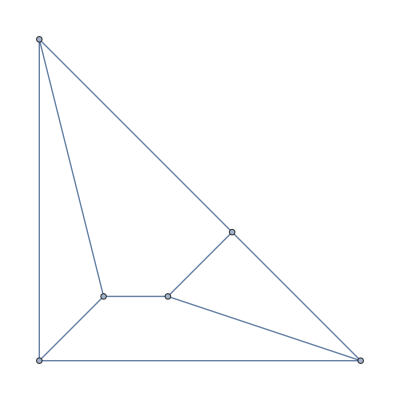

```mathematica
Graph[CompleteDual[ReadGraph[5,1]],GraphLayout->"PlanarEmbedding"]
```

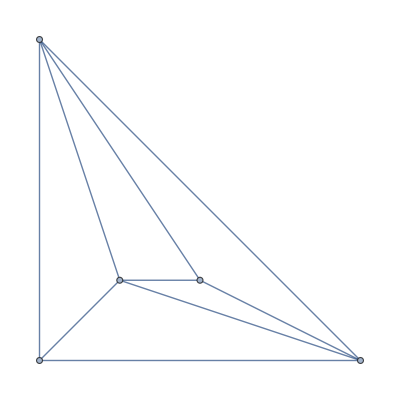

```mathematica
Graph[ReadGraph[5,1],GraphLayout->"PlanarEmbedding"]
```

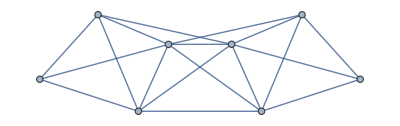

```mathematica
ReadGraph[8,1]
```

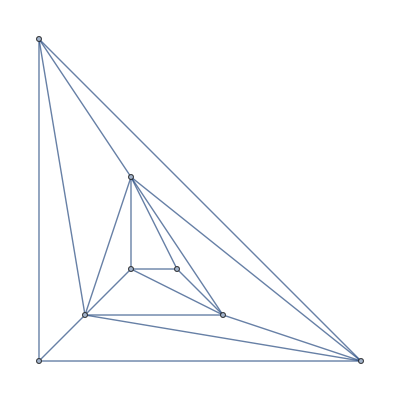
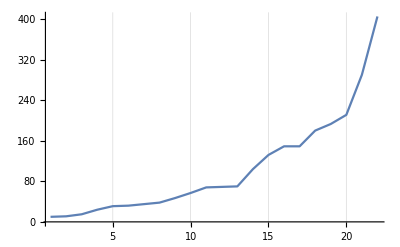
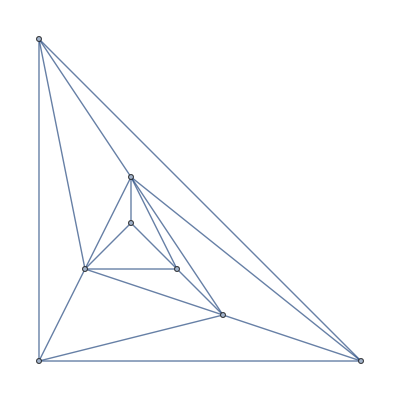
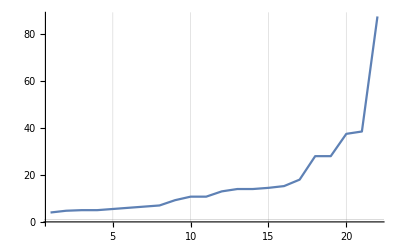
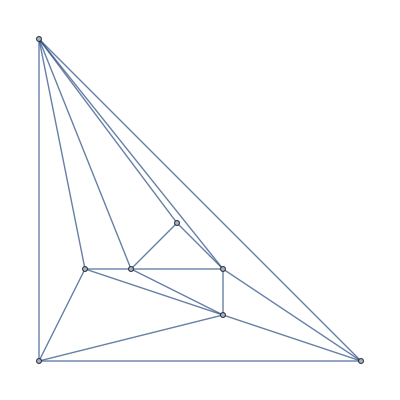
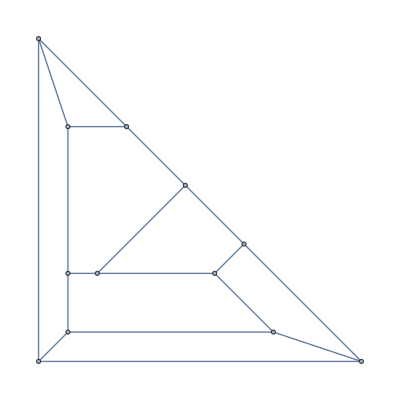
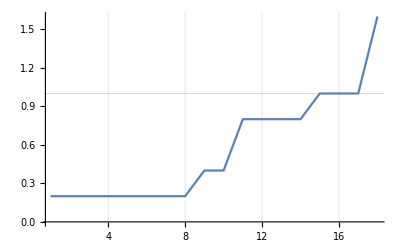
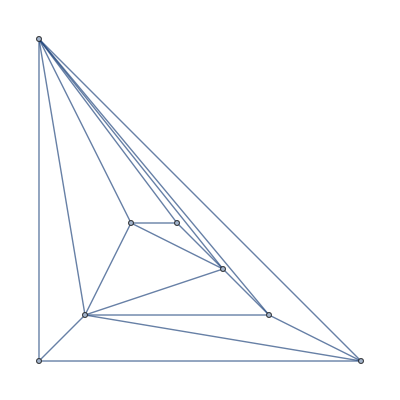
(-Graphics- |  | -Graphics-
-Graphics- |  | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- |  | -Graphics-
-Graphics- |  | -Graphics-)

```mathematica
Monitor[
MatrixForm[
Table[
With[
{g=ReadGraph[8,k]},
With[{base=ChromaticPolynomial[g,4], dual = CompleteDual[g]},
{
Graph[g, GraphLayout->"PlanarEmbedding"],
Graph[dual, GraphLayout->"PlanarEmbedding"],ListLinePlot[Sort[Table[ChromaticPolynomial[CompleteDual[ EdgeDelete[dual,e]],4]/base,{e,EdgeList[dual]}]],GridLines->{Automatic,{{1,{Thick,Red}}}},PlotRange->All]}
]
],
{k,Range[5]}
]
]
,k]
```

```mathematica
Faces[ReadGraph[8,1]]
```

{{1<->2,1<->3,2<->3},{1<->2,1<->8,2<->8},{1<->3,1<->8,3<->8},{2<->3,2<->5,3<->5},{2<->3,2<->6,3<->6},{2<->5,2<->6,5<->6},{4<->5,5<->6,4<->6},{2<->5,2<->8,5<->8},{3<->5,3<->7,5<->7},{4<->5,5<->7,4<->7},{3<->6,3<->7,6<->7}}

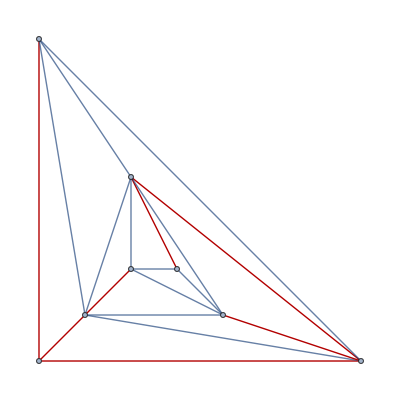

```mathematica
With[
{g=ReadGraph[8,1]},
Graph[g, GraphHighlight->SpanningTree[g], GraphLayout->"PlanarEmbedding"]
]
```